```mathematica
Quiet[<<Topy/vizhandmap.m]
```

```mathematica
rfs=readRFs["/Users/research2/projects/2013-topy/DM1.txt"];
```

```mathematica
lst=Map[First,rfs];
l1=RandomSample[lst,5];
l2=RandomSample[lst,5];
subset={l1,l2};
```

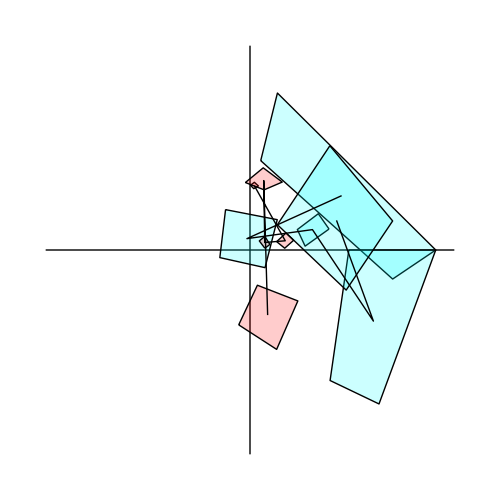

```mathematica
vizHandmap2[
rfs,
DisplayTracts->All,
PolygonCenterConnectorStyle->Black,
ImageSize->500,
VirtualTracts->subset
]
```